# Runge–Kutta Methods

Functionality for Runge–Kutta methods is provided under the Integreat`RK` context.

This loads the Runge–Kutta subpackage:

```mathematica
<<Integreat`RK`
```

## Basics

A Runge–Kutta method numerically approximates the solution of an initial value problem

y'(t)=f(t,y(t)),    y(t_0)=y_0 ,    t∈[t_0,t_f].

One step of a Runge–Kutta method is given by

Y_i=y_n+h∑_(j=1)^s a_(i,j)f(t_n+c_j h,Y_j),
y_(n+1)=y_n+h∑_(j=1)^s b_j f(t_n+c_j h,Y_j).

where h is the time step and y_(n+1)≈y(t_n+h). Some methods include an embedded solution to facilitate error estimation and time step adaptivity:

(ŷ)_(n+1)=y_n+h∑_(j=1)^s (b̂)_j f(t_n+c_j h,Y_j).

The coefficients which determine the Runge–Kutta method are often displayed as a Butcher tableau:

c_1 | a_(1,1) | a_(1,2) | ⋯ | a_(1,s)
c_2 | a_(2,1) | a_(2,2) | ⋯ | a_(2,s)
⋮ | ⋮ | ⋮ | ⋱ | ⋮
c_s | a_(s,1) | a_(s,2) | ⋯ | a_(s,s)
 | b_1 | b_2 | ⋯ | b_s
 | (b̂)_1 | (b̂)_2 | ⋯ | (b̂)_s

Integreat represents Runge–Kutta methods using the function RK. There are a number of constructors, but some of the primary are

RK[A,b,c] | constructs a Runge–Kutta method with coefficients A, b, and c.
RK[A,b] | constructs a Runge–Kutta method with c coefficients that are the row sum of A.
RK[A,b,c,bHat] | constructs an embedded Runge–Kutta pair.

Creating a Runge–Kutta method.

This creates Heun's method with forward Euler used as the embedding.

```mathematica
RK[{{0, 0}, {1, 0}},{1/2,1/2},{0,1},{1,0}]
```

0 | 0 | 0
1 | 1 | 0
 | 1/2 | 1/2
 | 1 | 0

Once a Runge–Kutta method is constructed, a wide range of properties can be queried. We start by showing how to recover the defining coefficients.

RKA[rk] | gives the A coefficients of the Runge–Kutta method rk.
RKB[rk] | gives the b coefficients of the Runge–Kutta method rk.
RKC[rk] | gives the c coefficients of the Runge–Kutta method rk.
RKBHat[rk] | gives the embedded coefficients of an embedded Runge–Kutta pair rk.

Access method coefficients.

Extract the coefficients from an embedded pair.

```mathematica
rk=RK["ode23"]
RKA[rk]
RKB[rk]
RKC[rk]
RKBHat[rk]
```

0 | 0 | 0 | 0 | 0
1/2 | 1/2 | 0 | 0 | 0
3/4 | 0 | 3/4 | 0 | 0
1 | 2/9 | 1/3 | 4/9 | 0
 | 2/9 | 1/3 | 4/9 | 0
 | 7/24 | 1/4 | 1/3 | 1/8

{{0,0,0,0},{1/2,0,0,0},{0,3/4,0,0},{2/9,1/3,4/9,0}}

{2/9,1/3,4/9,0}

{0,1/2,3/4,1}

{7/24,1/4,1/3,1/8}

There are three options defined for RKB which play a core role in Integreat's support for advanced features like embedded methods, dense output, and per-stage properties.

Embedded | False | whether to return the embedded coefficients
Stage | None | treat a stage as the solution
DenseOutput | False | how to evaluate dense output

Options for RKB.

Use options for RKB.

```mathematica
rk=RK[{{1/4, 0}, {1/2, 1/4}},{θ/2,θ/2},{0,3/4},{0,1}]
RKB[rk,Embedded->True]
RKB[rk,Stage->1]
RKB[rk,DenseOutput->True]
RKB[rk,DenseOutput->0.2]
```

0 | 1/4 | 0
3/4 | 1/2 | 1/4
 | 1/2 | 1/2
 | 0 | 1

{0,1}

{1/4,0}

{θ/2,θ/2}

{0.1,0.1}

Whenever appropriate, functions for computing Runge–Kutta properties use the same options as RKB. This facilitates, for example, plotting the stability region of an embedded method, generating the order conditions for a dense output solution, and checking the dissipation error of a particular Runge–Kutta stage. In the next sections, we will explore some of these capabilities.

## Order Conditions and Error Analysis

Deriving order conditions for Runge–Kutta methods by hand is a notoriously tedious and error-prone. Integreat uses B-trees to automate and simplify this process.

RKOrderConditions[rk,p] | generates the order condition residuals of rk up to order p grouped by order.
RKOrder[rk] | computes the order of accuracy of rk.
RKErrorA[rk] | computes the 2-norm of the principal error residuals of rk.

Select functions for order conditions.

Generate order conditions for a two stage Runge–Kutta method.

```mathematica
rk=RK[2]
RKOrderConditions[rk,3]
```

c_1 | a_(1,1) | a_(1,2)
c_2 | a_(2,1) | a_(2,2)
 | b_1 | b_2

{{-1+b_1+b_2},{-1/2+b_1 c_1+b_2 c_2},{-1/6+b_1 (c_1 a_(1,1)+c_2 a_(1,2))+b_2 (c_1 a_(2,1)+c_2 a_(2,2)),1/2 (-1/3+b_1 c_1^2+b_2 c_2^2)}}

Find the order of an embedded method.

```mathematica
rk=RK["ode23"]
RKOrder[rk,Embedded->True]
```

0 | 0 | 0 | 0 | 0
1/2 | 1/2 | 0 | 0 | 0
3/4 | 0 | 3/4 | 0 | 0
1 | 2/9 | 1/3 | 4/9 | 0
 | 2/9 | 1/3 | 4/9 | 0
 | 7/24 | 1/4 | 1/3 | 1/8

2

Once order conditions are generated, functions like Solve and SolveAlways can be used to find solutions. The parameterization of a method plays a significant role in how well these functions perform. We demonstrate this in the next two examples where we seek a family of explicit, third order Runge–Kutta methods.

This parameterization of a Runge–Kutta method leads to complicated solutions with branching.

```mathematica
rk=RK[{{0, 0, 0}, {Subscript[a, 2,1], 0, 0}, {Subscript[a, 3,1], Subscript[a, 3,2], 0}},{Subscript[b, 1],Subscript[b, 2],Subscript[b, 3]}]
Solve[RKOrderConditions[rk,3]==0]//Simplify
```

0 | 0 | 0 | 0
a_(2,1) | a_(2,1) | 0 | 0
a_(3,1)+a_(3,2) | a_(3,1) | a_(3,2) | 0
 | b_1 | b_2 | b_3

{{b_1→1-1/2 b_3 (1+6 a_(3,2)+√(1-12 a_(3,2)+48 b_3 a_(3,2)^2)),b_2→1/2 b_3 (-1+6 a_(3,2)+√(1-12 a_(3,2)+48 b_3 a_(3,2)^2)),a_(2,1)→1/(6 b_3 a_(3,2)),a_(3,1)→-(-1+12 b_3 a_(3,2)^2+√(1-12 a_(3,2)+48 b_3 a_(3,2)^2))/(12 b_3 a_(3,2))},{b_1→1+1/2 b_3 (-1-6 a_(3,2)+√(1-12 a_(3,2)+48 b_3 a_(3,2)^2)),b_2→-1/2 b_3 (1-6 a_(3,2)+√(1-12 a_(3,2)+48 b_3 a_(3,2)^2)),a_(2,1)→1/(6 b_3 a_(3,2)),a_(3,1)→(1-12 b_3 a_(3,2)^2+√(1-12 a_(3,2)+48 b_3 a_(3,2)^2))/(12 b_3 a_(3,2))}}

Here, the method is parameterized so that the row sum of A is c. When invoking Solve, the abscissae are left as free variables. We recommend this approach as it generally provides simpler and faster solutions.

```mathematica
rk=RK[{{0, 0, 0}, {Subscript[c, 2], 0, 0}, {Subscript[c, 3]-Subscript[a, 3,2], Subscript[a, 3,2], 0}},{Subscript[b, 1],Subscript[b, 2],Subscript[b, 3]}]
freeVars=Complement[Variables[rk],Variables[RKC[rk]]];
sols=Solve[RKOrderConditions[rk,3]==0,freeVars]
rk=rk/.First[sols];
```

0 | 0 | 0 | 0
c_2 | c_2 | 0 | 0
c_3 | c_3-a_(3,2) | a_(3,2) | 0
 | b_1 | b_2 | b_3

{{b_1→(2-3 c_2-3 c_3+6 c_2 c_3)/(6 c_2 c_3),b_2→(-2+3 c_3)/(6 c_2 (-c_2+c_3)),b_3→(-2+3 c_2)/(6 (c_2-c_3) c_3),a_(3,2)→((c_2-c_3) c_3)/(c_2 (-2+3 c_2))}}

With order conditions solved, free variables can be used to optimize other properties of the method. One common approach is minimizing the principal error.

Find the explicit, third order Runge–Kutta method with the smallest error:

```mathematica
min=Minimize[RKErrorA[rk],Variables[rk]]
rk=rk/.Rationalize[Last[N[min]],0.01]
```

{√(1/576+Root1.19 × 10^-5Root[-307+25803648 #1+1786364928 #1^2+34828517376 #1^3&,1]0.000011887756901869667),{c_2→Root0.497Root[{-307+25803648 #1+1786364928 #1^2+34828517376 #1^3&,20-11520 #1-86 #2+3456 #1 #2+109 #2^2-2592 #1 #2^2-42 #2^3+18 #2^4&},{1,2}]0.49650504476680324,c_3→Root0.752Root[{-307+25803648 #1+1786364928 #1^2+34828517376 #1^3&,20-11520 #1-86 #2+3456 #1 #2+109 #2^2-2592 #1 #2^2-42 #2^3+18 #2^4&,99-5184 #1-60 #2+52 #2^2-240 #3+68 #2 #3-48 #2^2 #3+160 #3^2-48 #2 #3^2+36 #2^2 #3^2&},{1,2,2}]0.7517474776165983}}

0 | 0 | 0 | 0
1/2 | 1/2 | 0 | 0
3/4 | 0 | 3/4 | 0
 | 2/9 | 1/3 | 4/9

## Stability Analysis

Linear stability analysis considers the behavior of a Runge–Kutta method applied to the Dahlquist test problem y'=λ y. The numerical solution for this problem is y_(n+1)=R(z)y_n, where

R(z)=1+bᵀ(I-z A)^-1 e

is the linear stability function and z=h λ. The set of z∈ℂ for which |R(z)|≤1 is known as the region of absolute stability. The size of the stability region determines the range of stable time steps a Runge–Kutta method can take.

RKLinearStability[rk,z] | evaluates the linear stability function of rk at z.
RKLinearStabilityPlot[rk] | plots the linear stability region of rk.
RKAStable[rk] | returns an algebraic condition equivalent to rk being stable in the left half-plane.

Select functions for linear stability analysis.

Check linear stability properties of the classical fourth order Runge–Kutta method.

0 | 0 | 0 | 0 | 0
1/2 | 1/2 | 0 | 0 | 0
1/2 | 0 | 1/2 | 0 | 0
1 | 0 | 0 | 1 | 0
 | 1/6 | 1/3 | 1/3 | 1/6

1+z+z^2/2+z^3/6+z^4/24

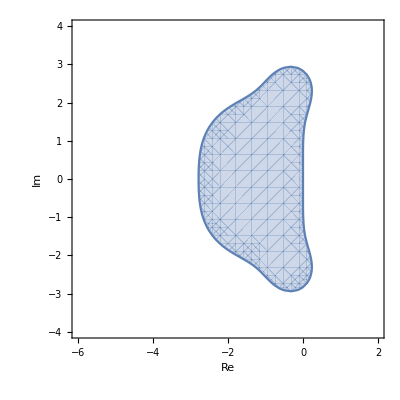

False

```mathematica
rk=RK["RK4"]
RKLinearStability[rk,z]//Simplify
RKLinearStabilityPlot[rk]
RKAStable[rk,Stage->3]
```

Integreat also include nonlinear stability analysis capabilities.

RKAlgebraicallyStableQ[rk] | returns True if rk is algebraically stable and False, otherwise.
RKAbsoluteMonotonicityRadius[rk] | computes the radius of absolute monotonicity, also known as the strong stability preserving (SSP) coefficient, of rk.

Select functions for nonlinear stability analysis.

Check nonlinear stability properties of a collocation method.

```mathematica
rk=RKCollocation[{0,1}]//Simplify
RKAlgebraicallyStableQ[rk]
RKAbsoluteMonotonicityRadius[rk,DenseOutput->True]//Simplify
```

0 | 0 | 0
1 | 1/2 | 1/2
 | 1/2 | 1/2

False

Piecewise[{{2, 0≤θ≤4/3}, {(2-θ)/(-1+θ), 4/3<θ<2}, {0, True}}]

## Extending the Runge–Kutta Framework

Advanced users may need to create custom functions to analyze Runge–Kutta methods. The patterns _RK and _?RKPairQ can be used to accept an RK object as a function argument. If a custom function uses the b coefficients of a method, it probably should accept RKB options.

A custom function to generate linear order condition residuals.

```mathematica
RKLinearOrderCondition[rk_RK,p_Integer,opts:OptionsPattern[RKB]]:=Total[NestList[#.RKA[rk]&,RKB[rk,opts],p-1],{2}]- 1/Range[p]!
```

Related Guides

Integreat Package

Runge–Kutta Methods

Linear Multistep Methods

General Linear Methods

Related Tech Notes

Integreat Package

Linear Multistep Methods

General Linear Methods

## Metadata

### Categorization

Tech Note

Integreat

Integreat`RK`

Integreat/tutorial/Runge-KuttaMethods

### Keywords